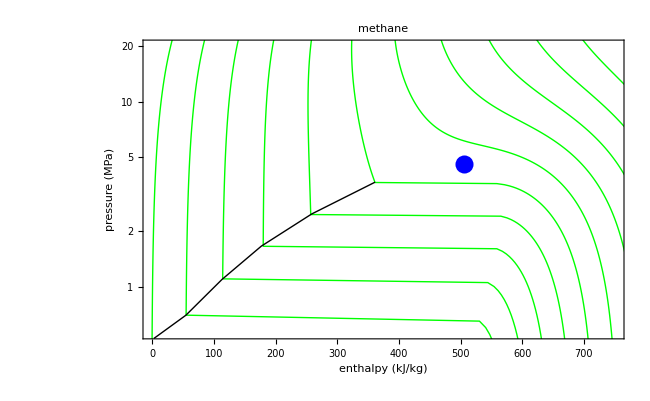

```mathematica
Module[{HL,HV,MW,R,Tref,Pref,Tc,Pc,CpA,CpB,CpC,CpD,Hig,Hdepref,ω,κ,A,B,a2,a1,a0,q,p,r,θ,Z,Hdep,H,p1,p2},

HL={(*{"HL","Pressure (MPa)"},*){85.54,0.5},{98.334,0.6},{109.82,0.7},{120.33,0.8},{130.05,0.9},{139.16,1.},{147.74,1.1},{155.9,1.2},{163.69,1.3},{171.17,1.4},{178.37,1.5},{185.34,1.6},{192.1,1.7},{198.69,1.8},{205.11,1.9},{211.39,2.},{217.55,2.1},{223.61,2.2},{229.57,2.3},{235.45,2.4},{241.26,2.5},{247.02,2.6},{252.74,2.7},{258.42,2.8},{264.08,2.9},{269.74,3.},{275.4,3.1},{281.08,3.2},{286.79,3.3},{292.55,3.4},{298.38,3.5},{304.31,3.6},{310.37,3.7},{316.58,3.8},{323.01,3.9},{329.71,4.},{336.79,4.1},{344.41,4.2},{352.84,4.3},{362.61,4.4},{375.26,4.5}};
HV={(*{"HV","Pressure (MPa)"},*){543.79,0.5},{547.18,0.6},{549.82,0.7},{551.91,0.8},{553.54,0.9},{554.81,1.},{555.77,1.1},{556.45,1.2},{556.9,1.3},{557.14,1.4},{557.18,1.5},{557.05,1.6},{556.75,1.7},{556.3,1.8},{555.69,1.9},{554.95,2.},{554.06,2.1},{553.05,2.2},{551.89,2.3},{550.6,2.4},{549.18,2.5},{547.62,2.6},{545.92,2.7},{544.08,2.8},{542.08,2.9},{539.93,3.},{537.61,3.1},{535.11,3.2},{532.42,3.3},{529.51,3.4},{526.37,3.5},{522.96,3.6},{519.25,3.7},{515.19,3.8},{510.72,3.9},{505.74,4.},{500.11,4.1},{493.63,4.2},{485.91,4.3},{476.22,4.4},{462.49,4.5}};

MW=16.04;(*kg/kmol*)
R=8.314/MW;(*kJ/kmol/K*)
Tref=298;Pref=0.1;
Tc=190.6;
Pc=4.604;

CpA=19.25;
CpB=0.05213;
CpC=1.197*10^-5;
CpD=1.132*10^-8;
Hig=(CpA*(T-Tref)+1/2*CpB*(T^2-Tref^2)+1/3*CpC*(T^3-Tref^3)+1/4*CpD*(T^4-Tref^4))/MW;
Hdepref=-18.1508/MW;

ω=0.011;
κ=0.37464+1.54226*ω-0.26992*ω^2;

A=0.4572355289*(1+κ*(1-√(T/Tc)))^2*(Tc^2*P)/(T^2*Pc);
B=0.0777960739*(P*Tc)/(Pc*T);

(*ROOTS*)
a2=B-1;
a1=A-3*B^2-2*B;
a0=-A*B+B^2+B^3;

q=(2*a2^3-9*a2*a1+27*a0)/27;
p=(3*a1-a2^2)/3;

r=q^2/4+p^3/27;

θ=ArcCos[(3*q)/(2*p*√(-p/3))]/3;
Z=Piecewise[{{CubeRoot[-q/2+√r]+CubeRoot[-q/2-√r]-a2/3,r>0},{2*√(-p/3)*Cos[θ]-a2/3,r≤0}}];
Hdep=R*T*(Z-1-A/(2.8284*B)*(1+κ*√(T/(Tc*(1+κ*(1-√(T/Tc)))^2)))*Log[(Z+2.4142*B)/(Z-0.4142*B)]);
H=Table[Table[{Hdep-Hdepref+Hig+958,P},{P,0.5,25,0.05}],{T,80,280,20}];


Show[
ListLogPlot[H,Joined->True,PlotStyle->{{Thick,Green}}],
(*ListLogPlot[{HL,HV},Joined->True,PlotStyle->{{Thick,Black}}],*)
Graphics[{
{Thick,
Line[{{361.351,Log@3.66544},{258.657,Log@2.46806},{176.763,Log@1.65192},{113.067,Log@1.09189},{54.5705,Log@0.699649},{2.57384,Log@0.523615}}]},
{Blue,PointSize[0.02],Point[{505,Log@Pc}]}
}],
Frame->True,FrameLabel->{Style["enthalpy (kJ/kg)",17],Style["pressure  (MPa)",17]},LabelStyle->{Black,14},
PlotRange->{{0,750},{Log@0.56,Log@20}},Axes->False,ImageSize->650,PlotLabel->Style["methane",18]]
]
```

```mathematica
{361.351,Log@3.66544},{258.657,Log@2.46806},{176.763,Log@1.65192},{113.067,Log@1.09189},{54.5705,Log@0.699649},{2.57384,Log@0.523615}
```

Syntax::tsntxi: "{361.351, Log @ 3.66544}, {258.657, Log @ 2.46806}, {176.763, Log @ 1.65192}, {113.067, Log @ 1.09189}, {54.5705, Log @ 0.699649}, {2.57384, Log @ 0.523615}" is incomplete; more input is needed.""

```mathematica
-3789/16.04+958
```

721.778

```mathematica
-7265.45/16.04+958
```

505.042